```mathematica
(*-----------------------*)
(* This file is copy of 5-1 (with behavioural changes in July2022) *)
(* but calculations continue until 31dec2022 *)
(*-----------------------*)
SetDirectory["N:\\mpoxPUB1\\codeMathematica\\num250"];
<<num250A\\param\\paramCertain; 
<<"0paramUncSel";    
dataAll=Flatten[Import["CasesPerOnsetDate.xls"]];
SetDirectory["N:\\mpoxPUB1\\codeMathematica\\num250\\resG1new"];
Tmax=249;
```

```mathematica
nsim=nSel
nmaxsimG=nmaxsim
```

198

23200

```mathematica
(*-------------------------------------------------------*)
(* initial conditions *) 
SUini=State0[[1]]; EUini=State0[[2]]; IUini=State0[[3]];YUini=State0[[4]];
SVini=State0[[5]]; EVini=State0[[6]]; IVini=State0[[7]];YVini=State0[[8]];
SPini=State0[[9]]; EPini=State0[[10]]; IPini=State0[[11]];YPini=State0[[12]];
RRini=State0[[13]]; HHini=State0[[14]]; 

(* total size of popul & infectious pop *)
Ntot[i_,t_]:=SU[i][t]+EU[i][t]+IU[i][t]+YU[i][t]+SV[i][t]+EV[i][t]+IV[i][t]+YV[i][t]+SP[i][t]+EP[i][t]+IP[i][t]+YP[i][t]+RR[i][t]+HH[i][t]; (*group i *)
Ntot[t_]:=Sum[Ntot[i,t],{i,1,ag}];    (* tot pop *)
Itot[t_]:=Sum[IU[i][t]+IV[i][t]+IP[i][t],{i,1,ag}];    (* total INFECTIOUS not-isolated *)
Ytot[t_]:=Sum[YU[i][t]+YV[i][t]+YP[i][t],{i,1,ag}];   (* total INFECTIOUS isolated *)
```

```mathematica
(*--------- VACCINATION BEFORE 25JULY2022 (CONTACTS OF CASES) ------------------*)
phi1d    =Izero;  (* vaccination of uninfected *)
phi2d    =Izero; (* vaccination of exposed *)
XTvac[t_]:=Piecewise[{{0,  t<42}, (* first 4w  *)
                                               {vacRate1,42≤t   }    }]
```

```mathematica
(*------------CHANGES IN JUNE/JULY ------------------------------------------*)
t1=57;t2=75;
casF4[t_]    :=Piecewise[{{0,t<t2},{cas4,t2≤t }}] ;
casF3[t_]    :=Piecewise[{{0,t<t2},{cas3,t2≤t }}] ;
casF2[t_]    :=Piecewise[{{0,t<t2},{cas2,t2≤t }}] ;

rateTOisolF[t_]  :=Piecewise[{{1/Tisol1,                                          t<t2},{1/Tisol3,t2≤t }}] ;
rateOUTisolF[t_]:=Piecewise[{{1/(infectiousDays-Tisol1),t<t2},{1/(infectiousDays-Tisol3),t2≤t }}] ;
```

```mathematica
(*----------------------- IMPORT INFECTIOUS CASES 1NOV2022 -----------------*)
t3=188; (* 1nov2022 *)
Ximpo[t_]:=Piecewise[{{0,  t<t3}, {1,t3≤t  }    }];
```

```mathematica
(************* LOOP ************)
Do[ (* START of loop of runs for each param set *)
t1=upSel[j,15];
t2=upSel[j,16];

theta             =1/upSel[j,1];
infectiousDays=upSel[j,2];  
Tisol1                  =upSel[j,12];
Tisol2                  =upSel[j,13];
Tisol3                  =upSel[j,14];delta=rateTOisolF[t];gamma=rateOUTisolF[t];  

betaS=upSel[j,3];
aC4   =upSel[j,4];aCbef={aCd[[1]],aCd[[2]],aCd[[3]],aC4};
cas2=upSel[j,17]; 
cas3=upSel[j,18]; 
cas4=upSel[j,19];
casB2=upSel[j,20]; 
casB3=upSel[j,21]; 
casB4=upSel[j,22];aCcha={casF2[t],casF2[t],casF3[t],casF4[t]};aC=aCbef-aCbef*aCcha;

w                =upSel[j,5];
epsilonM=upSel[j,6];
epsilonC=upSel[j,7];
vacRate1=upSel[j,8];phi1={0,0,XTvac[t],XTvac[t]}; phi2=phi1;
v1             =upSel[j,9];sigma1=v1;sigma1HAT=v1;(* oldVE *)
v2             =upSel[j,10];sigma2=v2; (*newVE *)
zeta        =upSel[j,11];

(* parameters for transm prob with sex partners *) 
Bs[k_,l_]  :=(1-        betaS)^((uM[[k]]+uM[[l]])/2);(* sex contacts with main partn *)
Bsv[k_,l_]:=(1-v1*betaS)^((uM[[k]]+uM[[l]])/2);
Bsp[k_,l_]:=(1-v2*betaS)^((uM[[k]]+uM[[l]])/2);

(* mixing *)
mM[i_,l_,t_]:=epsilonM*dd[i][[l]]+(1-epsilonM)*aM[[l]]*Ntot[l,t]/Sum[aM[[jp]]*Ntot[jp,t],{jp,1,ag}];
mC[i_,l_,t_]:=epsilonC*dd[i][[l]]+(1-epsilonC)*aC[[l]]*Ntot[l,t]/Sum[aC[[jp]]*Ntot[jp,t],{jp,1,ag}];

(* LAMBDA'S *)
lambdaM[i_,t_ ]:=q[[i]]*Sum[ mM[i,l,t]*((1-Bs[i,l])*(IU[l][t]+w*YU[l][t])+(1-Bsv[i,l])*(IV[l][t]+w*YV[l][t])+(1-Bsp[i,l])*(IP[l][t]+w*YP[l][t]))/Ntot[l,t],{l,1,ag}];
lambdaC[i_,t_ ]:=aC[[i]]*betaS*Sum[ mC[i,l,t]*((IU[l][t]+w*YU[l][t])+v1*(IV[l][t]+w*YV[l][t])+v2*(IP[l][t]+w*YP[l][t]))/Ntot[l,t],{l,1,ag}];
lambda[i_,t_ ]     :=lambdaM[i,t ]+lambdaC[i,t ];
lambdaFromAG[l_,i_,t_ ]:=q[[i]]* mM[i,l,t]*((1-Bs[i,l])*(IU[l][t]+w*YU[l][t])+(1-Bsv[i,l])*(IV[l][t]+w*YV[l][t])+(1-Bsp[i,l])*(IP[l][t]+w*YP[l][t]))/Ntot[l,t]
                                                      +aC[[i]]*betaS* mC[i,l,t]*((IU[l][t]+w*YU[l][t])+v1*(IV[l][t]+w*YV[l][t])+v2*(IP[l][t]+w*YP[l][t]))/Ntot[l,t];

(* SOLVE  *)
xequa=Join[
Table[SU[i]'[t]  ==-(mu+lambda[i,t]+phi1[[i]])*SU[i][t]+mu*Ntot[i,t],{i,ag}],
Table[EU[i]'[t]==-(mu+phi2[[i]]+theta)*EU[i][t]+lambda[i,t]*SU[i][t],{i,ag}],
Table[IU[i]'[t]==Ximpo[t]-(mu+mud+delta+zeta)*IU[i][t]+theta*EU[i][t],{i,ag}],
Table[YU[i]'[t]==-(mu+mud+gamma+zeta)*YU[i][t]+delta*IU[i][t],{i,ag}],
Table[SV[i]'[t]==-(mu+sigma1*lambda[i,t]+phi1[[i]])*SV[i][t],{i,ag}],
Table[EV[i]'[t]==sigma1HAT*lambda[i,t]*SV[i][t]-(mu+theta+phi2[[i]])*EV[i][t],{i,ag}],
Table[IV[i]'[t]==sigma1*theta*EV[i][t]-(mu+mud+delta+zeta)*IV[i][t],{i,ag}],
Table[YV[i]'[t]==delta*IV[i][t]-(mu+mud+gamma+zeta)*YV[i][t],{i,ag}],
Table[SP[i]'[t]==phi1[[i]]*(SU[i][t]+SV[i][t])-(mu+sigma2*lambda[i,t])*SP[i][t],{i,ag}],
Table[EP[i]'[t]==sigma2*lambda[i,t]*SP[i][t]+phi2[[i]]*(EU[i][t]+EV[i][t])-(mu+theta)*EP[i][t],{i,ag}],
Table[IP[i]'[t]==sigma2*theta*EP[i][t]-(mu+delta)*IP[i][t],{i,ag}],
Table[YP[i]'[t]==delta*IP[i][t]-(mu+gamma)*YP[i][t],{i,ag}],
Table[RR[i]'[t]  ==-mu*RR[i][t]+(1-sigma1)*theta*EV[i][t]+(1-sigma2)*theta*EP[i][t]+gamma*(Ytot[t]+HH[i][t]),{i,ag}],
Table[HH[i]'[t]  ==-(mu+mud+gamma)*HH[i][t]+zeta*(IU[i][t]+YU[i][t]+IV[i][t]+YV[i][t]),{i,ag}],


Table[SU[i][0]==SUini[[i]],{i,ag}],
Table[EU[i][0]==EUini[[i]],{i,ag}],
Table[IU[i][0]==IUini[[i]],{i,ag}],
Table[YU[i][0]==YUini[[i]],{i,ag}],
Table[SV[i][0]==SVini[[i]],{i,ag}],
Table[EV[i][0]==EVini[[i]],{i,ag}],
Table[IV[i][0]==IVini[[i]],{i,ag}],
Table[YV[i][0]==YVini[[i]],{i,ag}],
Table[SP[i][0]==SPini[[i]],{i,ag}],
Table[EP[i][0]==EPini[[i]],{i,ag}],
Table[IP[i][0]==IPini[[i]],{i,ag}],
Table[YP[i][0]==YPini[[i]],{i,ag}],
Table[RR[i][0]==RRini[[i]],{i,ag}],
Table[HH[i][0]==HHini[[i]],{i,ag}]           ];
xvar=Join[Flatten[Table[{SU[i],EU[i],IU[i],YU[i],SV[i],EV[i],IV[i],YV[i],SP[i],EP[i],IP[i],YP[i],RR[i],HH[i]},{i,ag}]] ];
xresult=NDSolve[xequa,xvar,{t,0,Tmax},MaxSteps->50000];  

(* epidemic outcomes to keep from selected runs *)
nSympFUN[t_]:=Sum[theta*(EU[i][t]+sigma1*EV[i][t]+sigma2*EP[i][t]),{i,1,ag}]; 
nSympEle[j]=(nSympFUN[t]/.xresult)[[1]];

If[Mod[j,100]==0 ,Print[j]],
 {j,1,nsim}];(* END of loop of runs for each param set *)
```

100

```mathematica
(*----- time points ------*)
tpoint=Table[it,{it,0,Tmax,1}];ntpoints=Length[tpoint];

(*----- save number daily cases --------*)
Do[t=tpoint[[it]];
nSymp[it]=Table[Evaluate[nSympEle[js]],{js,nsim}];  
nSympAll[it]=Flatten[Table[Table[nSymp[it][[j]],rSel[[j]]] ,{j,nsim}]];
,{it,1,ntpoints}];
```

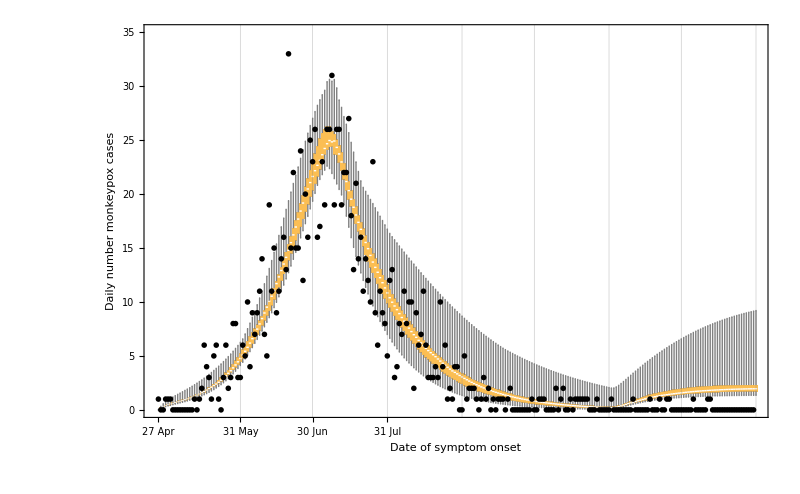

```mathematica
Show[ 
BoxWhiskerChart[Table[Table[nSympAll[it][[j]], {j,nmaxsim}],{it,Tmax}],PlotRange->{{0,Tmax},{0,35}},BaseStyle->{FontFamily->"Arial",FontSize->14},GridLines->{{35,65,96,127,157,188,218,249},{50,55}},
ChartLabels->{"27 Apr","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","31 May","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","30 Jun","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","31 Jul","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","31 Aug","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","30 Sep","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","31 Oct","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","30 Nov","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","","31 Dec"},Frame->{True,True,False,False},FrameLabel->{"Date of symptom onset","Daily number monkeypox cases"}],
ListPlot[Table[{it,dataAll[[it]]},{it,1,Length[dataAll]}],PlotStyle->{Black,PointSize[.005]},Joined->False],
ImageSize->800]
```

```mathematica
Do[t=tpoint[[it]];
cumSymp[it]=Sum[nSymp[kk],{kk,1,it}];
cumSympAll[it]=Sum[nSympAll[kk],{kk,1,it}];
,{it,1,ntpoints}];
```

```mathematica
(*********************************************************************)
(* difference at Tmax from scenar without import *)
<<sens31dec1;    
Do[t=tpoint[[it]];nSympAll1[it]=Flatten[Table[Table[nSymp1[it][[j]],rSel[[j]]] ,{j,nSel}]],{it,1,ntpoints}];
cumSympAll1[Tmax]=Sum[nSympAll1[kk],{kk,1,Tmax}];
cumSympAll[Tmax]   =Sum[nSympAll[kk]  ,{kk,1,Tmax}];
dif=cumSympAll[Tmax]-cumSympAll1[Tmax];
Print[{Median[dif], Quantile[dif,.025],Quantile[dif,.975]}]
```

{80.9775,62.9323,210.702}

```mathematica
(***********************************************END*********************)
```